Dodelson 7.11

#### Exercise 7.11

Clear::wrsym: Symbol TraditionalForm`D is Protected.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after TraditionalForm`9 recursive bisections in TraditionalForm`x near TraditionalForm`{x} = TraditionalForm`{-1.00283}. NIntegrate obtained TraditionalForm`34.3  + 3846.53\ ⅈ and TraditionalForm`3803.8575892254657` for the integral and error estimates.

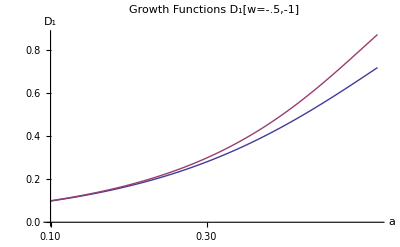

We plot the growth function for w=-.5 and -1 cases.

```mathematica
Clear[H,D]
Subscript[D, 1][a_]:=(5 Subscript[Ω, m])/2 H[a]/Subscript[H, 0]∫_0^a 1/(x H[x]/Subscript[H, 0])^3 ⅆx
H[a_]:= Subscript[H, 0] (Subscript[Ω, m]/a^3+Subscript[Ω, m]/a^(3(1+w)))^(1/2)
rules={Subscript[Ω, m]->.7,Subscript[Ω, de]->.3,w->-.5};
Hnew[a_]:=H[a]/.rules
Subscript[D, 1][a_]:=(5 Subscript[Ω, m])/2 Hnew[a]/Subscript[H, 0] NIntegrate[1/(x Hnew[x]/Subscript[H, 0])^3,{x,0,a}]/.rules

rules2={Subscript[Ω, m]->.7,Subscript[Ω, de]->.3,w->-1};
Hnew2[a_]:=H[a]/.rules2
Subscript[newD, 1][a_]:=(5 Subscript[Ω, m])/2 Hnew2[a]/Subscript[H, 0] NIntegrate[1/(x Hnew2[x]/Subscript[H, 0])^3,{x,0,a}]/.rules2
LogLinearPlot[{Tooltip[Subscript[D, 1][a],"w=-.5"],Tooltip[Subscript[newD, 1][a],"w=-1"]},{a,.1,1},AxesOrigin->{.1,0},

AxesLabel->{"a","D_1"},PlotLabel->"Growth Functions D_1[w=-.5,-1]"]
Print["We plot the growth function for w=-.5 and -1 cases."]
```